# Komal Aftab MSC(Final Year) Seat no:H1616066 Course no:632 “Mathematica Assignment”

## Chapter::1 First Order ODEs

## 1.1 General Solutions

```mathematica
Clear[y]
```

```mathematica
ode =y'[x]-3y[x]==0
```

-3 y[x]+y'[x]==0

```mathematica
DSolve[ode,y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]}}

```mathematica
sol =DSolve[ode,y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]}}

```mathematica
ypartic=DSolve[{ode,y[0]==2},y[x],x]
```

{{y[x]→2 ⅇ^(3 x)}}

```mathematica
y1 =c Exp[3 x];
```

```mathematica
D[y1,x]-3y1
```

0

```mathematica
ypartic/. x-> 0
```

{{y[0]→2}}

```mathematica
ypartic[[1,1]]
```

y[x]→2 ⅇ^(3 x)

```mathematica
ypartic[[1,1,2]]
```

2 ⅇ^(3 x)

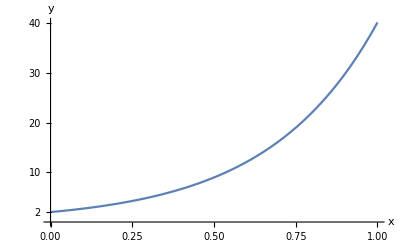

```mathematica
Plot[ypartic[[1,1,2]],{x,0,1},AxesLabel->{x,y},Ticks-> {Automatic,{2,10,20,30,40}}]
```

## 1.2 Direction Fields::

```mathematica
Clear[ode]
```

```mathematica
ode =y'[x]==x   y[x]
```

y'[x]==x y[x]

```mathematica
inits ={{0,1},{0,2}}
```

{{0,1},{0,2}}

VectorFieldPlot::shdw: Symbol VectorFieldPlot appears in multiple contexts {VectorFieldPlots`,Global`}; definitions in context VectorFieldPlots` may shadow or be shadowed by other definitions.

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

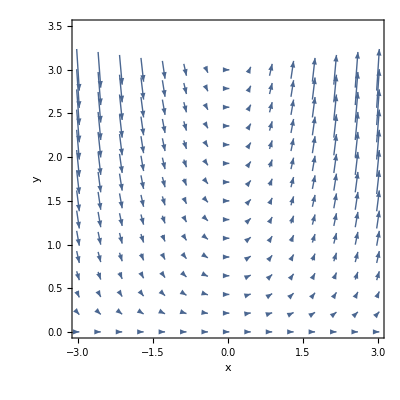

```mathematica
p1=VectorPlot[{1,x y},{x,-3,3},{y,0,3},AxesLabel->{x,y},Axes->True,PlotRange->{{-3,3},{0,3.5}}]
```

```mathematica
sol1 =DSolve[{ode,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(x^2/2)}}

```mathematica
sol2 =DSolve[{ode,y[0]==2},y[x],x]
```

{{y[x]→2 ⅇ^(x^2/2)}}

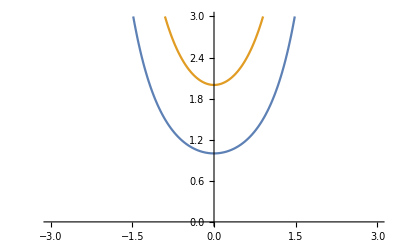

```mathematica
p2 =Plot[{sol1[[1,1,2]],sol2[[1,1,2]]},{x,-3,3},PlotRange->{0,3}]
```

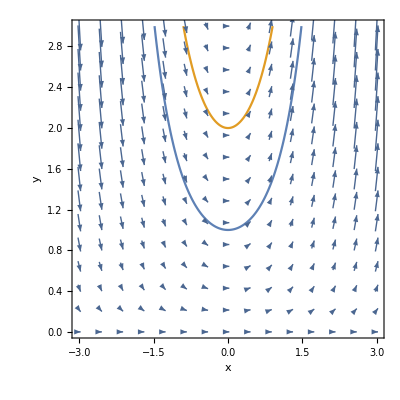

```mathematica
Show[p1,p2,PlotRange->{0,3},AxesLabel->{x,y},Axes->True]
```

## Mixing Problems::

```mathematica
Clear[ode]
```

```mathematica
ode =y'[t]==10 -(5/200) y[t]
```

y'[t]==10-y[t]/40

```mathematica
DSolve[{ode ,y[0]==40},y[t],t]
```

{{y[t]→40 ⅇ^(-t/40) (-9+10 ⅇ^(t/40))}}

```mathematica
ypartic1 =Simplify[%]
```

{{y[t]→400-360 ⅇ^(-t/40)}}

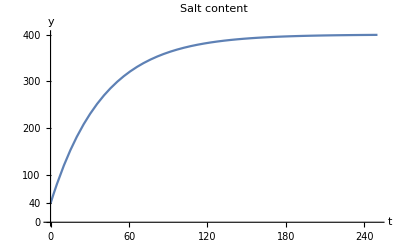

```mathematica
Plot[ypartic1[[1,1,2]],{t,0,250},PlotRange->{0,400},AxesLabel->{t,y},PlotLabel->"Salt content", Ticks->{Automatic,{0,40,100,200,300,400}}]
```

## 1.4 Integrating Factors::

```mathematica
p =2Sin[y^2]
```

2 Sin[y^2]

```mathematica
Q =x               y Cos[y^2]
```

x y Cos[y^2]

```mathematica
D[p,y]-D[Q,x]
```

3 y Cos[y^2]

```mathematica
eq1 =D[F[x]p,y]-D[F[x] Q,x]==0
```

3 y Cos[y^2] F[x]-x y Cos[y^2] F'[x]==0

```mathematica
Simplify[%]
```

y Cos[y^2] (3 F[x]-x F'[x])==0

```mathematica
Simplify[eq1][[1,3]]==0
```

3 F[x]-x F'[x]==0

```mathematica
sol3 =DSolve[%,F[x],x]
```

{{F[x]→x^3 C[1]}}

```mathematica
Integrate[x^3 p ,x]
```

1/2 x^4 Sin[y^2]

## 1.5 Bernoulli’s Equation::

```mathematica
Clear[ode,sol,sol1,sol2,sol3]
```

```mathematica
ode =Y'[x] ==A y[x]-B y[x]^2
```

Y'[x]==A y[x]-B y[x]^2

```mathematica
sol =DSolve[ode,y[x],x]
```

{{y[x]→(A-√(A^2-4 B Y'[x]))/(2 B)},{y[x]→(A+√(A^2-4 B Y'[x]))/(2 B)}}

```mathematica
sol2 =sol/.{A-> 1,B-> 1}
```

{{y[x]→1/2 (1-√(1-4 Y'[x]))},{y[x]→1/2 (1+√(1-4 Y'[x]))}}

```mathematica
y11 =sol2 /.Exp[C[1]]-> 9
```

{{y[x]→1/2 (1-√(1-4 Y'[x]))},{y[x]→1/2 (1+√(1-4 Y'[x]))}}

```mathematica
y2 =sol2/.Exp[C[1]]-> 0
```

{{y[x]→1/2 (1-√(1-4 Y'[x]))},{y[x]→1/2 (1+√(1-4 Y'[x]))}}

```mathematica
y3  =sol2/. Exp[C[1]] -> -0.5
```

{{y[x]→1/2 (1-√(1-4 Y'[x]))},{y[x]→1/2 (1+√(1-4 Y'[x]))}}

```mathematica
Plot[{y1[[1,1,2]],y2[[1,1,2]],y3[[1,1,2]]},
{x,0,5},PlotRange-> {0,2,3},AxesLabel->{x,y},Ticks->{Automatic,{0,0.5,1,1.5,2}},
PlotLabel->"Verhulat Population model"]
```

General::prng: Value of option PlotRange -> {0,2,3} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partd: Part specification (1.00031 c)⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification (1.35856 c)⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification (1.84513 c)⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

## RL-Circit::

```mathematica
Clear[ode,sol]
```

```mathematica
ode =l'[t]+50l[t]==110 Cos[3 t]
```

50 l[t]+l'[t]==110 Cos[3 t]

```mathematica
sol = DSolve[{ode,l[0]== 0},l[t],t]
```

{{l[t]→(110 ⅇ^(-50 t) (-50+50 ⅇ^(50 t) Cos[3 t]+3 ⅇ^(50 t) Sin[3 t]))/2509}}

```mathematica
sol21 =Expand[sol[[1,1,2]]]
```

-(5500 ⅇ^(-50 t))/2509+(5500 Cos[3 t])/2509+(330 Sin[3 t])/2509

```mathematica
N[%]
```

-2.19211 2.71828^(-50. t)+2.19211 Cos[3. t]+0.131527 Sin[3. t]

```mathematica
SetPrecision[sol21,4]
```

-2.192 2.718^(-50. t)+2.192 Cos[3. t]+0.1315 Sin[3. t]

## ----------------------DONE-------------------------